# [WSS20] Graph Representation of Biological Evolution

## Function Dictionary

```mathematica
?GraphToSuccessorAssociation
```

```mathematica
?SuccessorAssociationToGraph
```

```mathematica
?generationSuccessorFunction
```

```mathematica
?selectionSuccessorFunction
```

```mathematica
?GraphSignature
```

```mathematica
?IsomorphicGraphRepresentatives
```

```mathematica
?GraphPathMultiwaySystem
```

```mathematica
?GenerationGraph
```

```mathematica
?AllDirectedGraphs
```

```mathematica
?SelectionGraph
```

```mathematica
?EvolutionGraph
```

## Tool Box (Supporting Functions)

```mathematica
Get["GeneralUtilities`"]
MultiwaySystem := ResourceFunction["MultiwaySystem"]
```

### Graph Size, Organization etc.

```mathematica
niceEdgeShapeFunction[size_][coords_, d_DirectedEdge] := 
	GraphElementData[{"ShortFilledArrow","ArrowSize" -> size}][coords, d];
niceEdgeShapeFunction[size_][coords_, _] := Line[coords];
graphVertexCount[graph_Graph, ___] := VertexCount[graph];
graphVertexCount[edges_List, ___] /; !FreeQ[edges, DirectedEdge | UndirectedEdge | Rule | TwoWayRule] := 
	CountDistinct[Join[edges[[All, 1]], edges[[All, 2]]]];
graphVertexCount[vertices_List, edges_List, ___] := Length[vertices];
graphVertexCount[___] := 1;
countToSize[n_] := Which[
	n ≤ 3, 0.75, n ≤ 4, 0.8, n ≤ 5, 1, n ≤ 6, 1.5, n ≤ 7, 1.8, n ≤ 10, 2.0, n ≤ 15, 2.5, 
	n ≤ 50, 3, n ≤ 100, 4, True, 5];
countToEdgeSize[n_] := Which[
	n ≤ 3, .15, n ≤ 8, .1, n ≤ 12, .075, n ≤ 16, .05, True, .025];
NiceGraph[args___] := With[{count = graphVertexCount[args]}, Graph[args,
	VertexStyle -> {EdgeForm[GrayLevel[0, .2]]},
	EdgeShapeFunction -> niceEdgeShapeFunction[countToEdgeSize[count]],
	GraphLayout -> {"VertexLayout" -> "SpringElectricalEmbedding", "PackingLayout"->"ClosestPackingCenter"},
	EdgeStyle -> Gray, ImageSize -> {100, 100} * countToSize[count], 
	Background -> GrayLevel[0.97], PlotRangePadding -> 0.25
]];
```

### Colors

```mathematica
makeSegments[n_, center_ : {0, 0}, size_ : {1, 1}] := 
 makeSegments[n] = 
  Table[Disk[center, size, {i, i + 1}*2 Pi/n], {i, 1, n}]
singleton[l_List] := l
singleton[expr_] := {expr}
vecWheel[vec_, center_, size_] := 
 Thread@Style[makeSegments[Length[singleton@vec], center, size], 
   singleton@vec]
ColorGraph[args___]:=NiceGraph[args, 
  VertexShapeFunction -> (vecWheel[#2, #1, #3] &), VertexSize -> 0.5]
```

```mathematica
HueColors[n_] := Table[Hue[i/(n+1),.8,1], {i,0,n-1}];
```

```mathematica
HypercubeColorGraph[colors_] := Scope[
	n = Length[colors];
	logn = Log2[n];
	If[!IntegerQ[logn], Return[$Failed]];
	ColorGraph @ AdjacencyGraph[colors, AdjacencyMatrix @ HypercubeGraph[logn]]
]
```

### Graph Association Relationships

```mathematica
Options[GraphToSuccessorAssociation] = {
	"IncludeSelf" -> False
};
GraphToSuccessorAssociation[graph_, OptionsPattern[]] := Scope[
	vertices = VertexList[graph];
	n = Length[vertices];
	adjacency = Normal @ AdjacencyMatrix[graph];
	If[OptionValue["IncludeSelf"], adjacency += IdentityMatrix[n]];
	association = <||>;
	Do[
		association[vertices⟦i⟧] = Pick[vertices, adjacency⟦i⟧, 1],
		{i, n}
	];
	association
];
SetUsage[GraphToSuccessorAssociation,"GraphToSuccessorAssociation[graph$, opts$] takes a graph$ and for each vertex returns the possible successors in an association based on the directionality of edges"];

SuccessorAssociationToGraph[assoc_, opts___] := Graph[
	Keys[assoc],
	Flatten[Function[{src, dsts}, Map[src -> #&, dsts]] @@@ Normal[assoc]],
	opts
];
SetUsage[SuccessorAssociationToGraph,"SuccessorAssociationToGraph[association$, opts$] takes an association$ and returns the graph where the edges are directed from the keys to the values."];
```

### Generation Vector Successors

```mathematica
generationSuccessorFunction[generationVector_, mutations_] := With[
	{n = Length[generationVector]},
	Map[
		If[MemberQ[generationVector, #], Nothing,
			Sort @ Append[generationVector, #]]&,
		Union @@ Lookup[mutations, generationVector]
	] 
];
SetUsage[generationSuccessorFunction,"generationSuccessorFunction[generationVector$, mutations$] takes a generation$ vector$ and a successor association which reflects the valid mutations$ and outputs the valid generation vector successors."];

selectionSuccessorFunction[generationVector_, deletions_] := With[
	{n = Length[generationVector]},
	Map[
		If[!MemberQ[generationVector, #], Nothing,
			DeleteCases[generationVector, #]]&,
		Union @@ Lookup[deletions, generationVector]
	] 
];
SetUsage[selectionSuccessorFunction, "selectionSuccessorFunction[generationVector$, deletions$] takes a generation$ vector$ and a successor association which reflects the valid deletions$ and outputs the valid generation vector successors."];
```

### Graph Characteristics

```mathematica
vectorAng[a_, b_] := Quiet @ Check[Round[Dot[a, b], 0.001], None];
GraphSignature[graph_] := Module[{adj,evecs},
	adj = WeightedAdjacencyMatrix[graph];
	evecs = N @ Eigenvectors[adj];
	evecs = Join[evecs, -evecs];
	{Eigenvalues[adj], Sort[vectorAng @@@ Subsets[evecs, {2}]], 
		Length @ GraphSources @ graph, 
		Length @ GraphSinks @ graph,
		GraphDiameter @ graph,
		GraphRadius @ graph,
		KeySort @ Counts[Flatten @ GraphDistanceMatrix @ graph]}
];
SetUsage[GraphSignature,"GraphSignature[graph$] returns the number of a graphs$ sources and sinks, it's diameter, radius and the counts of the graph's$ distance matrix."];
IsomorphicGraphRepresentatives[graphs_] := 
	First/@Values[GroupBy[graphs, GraphSignature]];
SetUsage[IsomorphicGraphRepresentatives, "IsomorphicGraphRepresentatives[graphs$] checks for the graphs$ signatures, groups the similar ones and then only shows the first."];
```

## Main Functions

### Unrolling a Graph to its Multiway System

```mathematica
Options[GraphPathMultiwaySystem] = Prepend[
	Options @ MultiwaySystem, 
	"IncludeSelfMoves" -> True
];
GraphPathMultiwaySystem[graph_, All, args___, opts:OptionsPattern[]] := 
	GraphPathMultiwaySystem[graph, VertexList[graph], args, opts];
	
stepIdFixer[f_][sn_ -> state_] := Thread[(sn + 1) -> f[state]];

GraphPathMultiwaySystem[graph_, args___, opts:OptionsPattern[]] := Scope[
	UnpackOptions[includeSelfMoves];
	successorAssociation = GraphToSuccessorAssociation[graph, "IncludeSelf" -> includeSelfMoves];
	MultiwaySystem[<|
		"StateEvolutionFunction" -> stepIdFixer[successorAssociation],
		"StateEquivalenceFunction" -> SameQ,
		"StateEventFunction" -> Identity,
		"EventDecompositionFunction" -> Identity,
		"EventApplicationFunction" -> Identity,
		"SystemType" -> "StringSubstitutionSystem",
		"EventSelectionFunction" -> Identity|>,
		args,
		"IncludeStepNumber" -> True,
		opts
	]
];
SetUsage[GraphPathMultiwaySystem,"GraphPathMultiwaySystem[graph$, args$, opts$] takes a graph$ and extends it such that in each row the vertices connect to all valid successors, as determined in the graph, in the row below."];
```

### Generation Graph

```mathematica
GenerationGraph[mutationGraph_] := Module[
	{genotypes, generationVectors, mutations, successorAssociation},
	genotypes = VertexList[mutationGraph];
	generationVectors = Subsets[Sort @ genotypes, {1, Length[genotypes]}];
	mutations = GraphToSuccessorAssociation[mutationGraph, "IncludeSelf" -> False];
	(* allowedMutants association maps a genotype to a list of distance ≤ 1 genotypes *)
	successorAssociation = AssociationMap[generationSuccessorFunction[#, mutations]&, generationVectors];
	NiceGraph @ SuccessorAssociationToGraph[successorAssociation, Options[mutationGraph]]
];
SetUsage[GenerationGraph, "GenerationGraph[mutationGraph$] translates the valid mutations, as represented in the mutation$ graph$ and shows the resulting valid generation level updates (genetic drift)."];
```

### Enumerate Fitness and Mutation Graphs

```mathematica
AllDirectedGraphs[graph_] := Scope[
	edges = EdgeList[graph];
	verts = VertexList[graph];
	opts = Options[graph];
	n = Length[edges];
	edgeChoices = Function[{a, b}, {a -> b, b -> a, a <-> b, None}] @@@ edges;
	Graph[verts, DeleteNone[#], opts]& /@ Tuples[edgeChoices]
];
SetUsage[AllDirectedGraphs, "AllDirectedGraphs[graph$] returns all possible variations of the graph$ where the edges can be undirected, not existent or directed towards either vertix."];
```

### Selection Graph

```mathematica
SelectionGraph[fitnessGraph_] := Module[
	{genotypes, generationVectors, deletions, successorAssociation},
	genotypes = VertexList[fitnessGraph];
	generationVectors = Subsets[Sort @ genotypes, {1, Length[genotypes]}];
	deletions = GraphToSuccessorAssociation[ReverseGraph[fitnessGraph], "IncludeSelf" -> False];
	(* allowedMutants association maps a genotype to a list of distance ≤ 1 genotypes *)
	successorAssociation = AssociationMap[selectionSuccessorFunction[#, deletions]&, generationVectors];
	NiceGraph @ SuccessorAssociationToGraph[successorAssociation, Options[fitnessGraph]]
];
SetUsage[SelectionGraph, "SelectionGraph[fitnessGraph$] translates the valid deletions, as represented in the fitness$ graph$ and shows the resulting valid generation level updates (selection)."];
```

### Evolution Graph

```mathematica
EvolutionGraph[mutationGraph_,fitnessGraph_] := 
	ColorGraph@GraphUnion[GenerationGraph[mutationGraph], SelectionGraph[fitnessGraph]];
SetUsage[EvolutionGraph, "EvolutionGraph[mutationGraph$, fitnessGraph$] creates the generation level updates based on a mutation$ graph$ and a fitness$ graph$ (evolution)."];
```

## Demonstrations (if you want to check all the code is running smoothly, here are some checks)

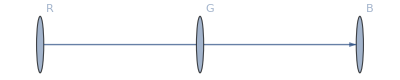

```mathematica
mutationGraph=Graph[{"R"<-> "G","G"->"B"}, VertexLabels->Automatic]
```

```mathematica
GraphToSuccessorAssociation[mutationGraph, "IncludeSelf" -> False]
```

<|R→{G},G→{R,B},B→{}|>

```mathematica
SuccessorAssociationToGraph[GraphToSuccessorAssociation[mutationGraph, "IncludeSelf" -> False]]
```

-Graphics-

```mathematica
GraphPathMultiwaySystem[
	mutationGraph, All, 4, "StatesGraph", 
	"IncludeStatePathWeights"->True, VertexLabels->"VertexWeight"]
```

-Graphics-

```mathematica
rgb=ColorGraph[{Red<->Green,Green<->Blue}]
```

-Graphics-

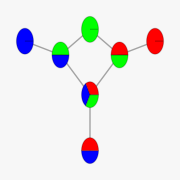

```mathematica
GenerationGraph[rgb]
```

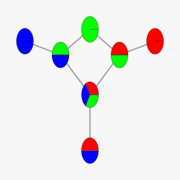

```mathematica
SelectionGraph[rgb]
```

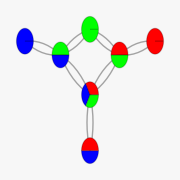

```mathematica
EvolutionGraph[rgb,rgb]
```

```mathematica
allgraphs=AllDirectedGraphs[ColorGraph[{Red<->Green,Green<->Blue,Blue<->Red}]];
```

```mathematica
fitnessreps=IsomorphicGraphRepresentatives[allgraphs]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Column[{#,SelectionGraph[#]}]& /@ fitnessreps;
```

## Explorations

### Two Genotype System

```mathematica
mutgraphs=Drop[AllDirectedGraphs[ColorGraph[{Red<-> Blue}]],-1];
```

```mathematica
fitgraphs=AllDirectedGraphs[ColorGraph[{Red<->Blue}]];
```

```mathematica
evoGrid=Table[EvolutionGraph[x,y],{y,fitgraphs},{x,mutgraphs}];
Grid[
Prepend[
MapThread[Prepend,{evoGrid,fitgraphs}],
Prepend[mutgraphs,Item[Grid[{{},{"","","m"},{},{"f","",""}}],Alignment->{Bottom,Right}]]
],
Dividers->{{False,True},{False,True}}
]
```

|  | 
 |  | m
 |  | 
f |  |  | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
IsomorphicGraphRepresentatives[Flatten[Table[EvolutionGraph[x,y],{y,fitgraphs},{x,mutgraphs}]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Row[Column[{#,Row[GraphSinks[#], " "]},Alignment->Center]&/@IsomorphicGraphRepresentatives[Flatten[Table[EvolutionGraph[x,y],{y,fitgraphs},{x,mutgraphs}]]]," "]
```

-Graphics-
  {RGBColor[0, 0, 1]}-Graphics-
  {RGBColor[1, 0, 0]}-Graphics-
  -Graphics-
  {RGBColor[0, 0, 1]}-Graphics-
  -Graphics-
  {RGBColor[0, 0, 1]}{RGBColor[0, 0, 1],RGBColor[1, 0, 0]}-Graphics-
  {RGBColor[0, 0, 1],RGBColor[1, 0, 0]}

```mathematica
Row[Column[{#,Row[GraphSinks[#], " "]},Alignment->Center]&/@Flatten[Table[EvolutionGraph[{Red<->Blue},y],{y,fitgraphs}],1]," "]
```

-Graphics-
  -Graphics-
  -Graphics-
  -Graphics-
  {RGBColor[0, 0, 1],RGBColor[1, 0, 0]}

```mathematica
Row[Column[{#,Row[GraphSinks[#], " "]},Alignment->Center]&/@Flatten[Table[EvolutionGraph[y,ColorGraph[{Red-> Blue}]],{y,mutgraphs}],1]," "]
```

-Graphics-
  {RGBColor[0, 0, 1]}-Graphics-
  -Graphics-
  {RGBColor[0, 0, 1]}{RGBColor[1, 0, 0]}

### Three Genotype System

```mathematica
allfitgraphs=AllDirectedGraphs[ColorGraph[{Red<->Green,Green<->Blue,Blue<->Red}]];
```

```mathematica
fitnessreps=IsomorphicGraphRepresentatives[allgraphs]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

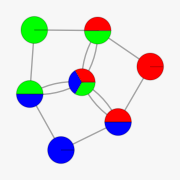
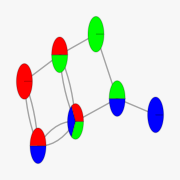
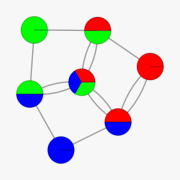
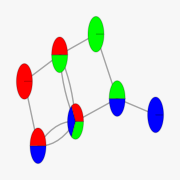
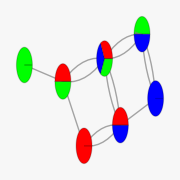
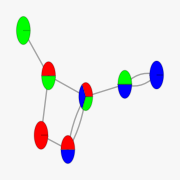
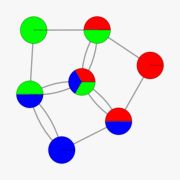
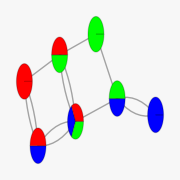
|  | 
 |  | m
 |  | 
f |  |  | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
evoGridthree=Table[EvolutionGraph[x,y],{y,fitnessreps},{x,fitnessreps}];
Grid[
Prepend[
MapThread[Prepend,{evoGridthree,fitnessreps}],
Prepend[fitnessreps,Item[Grid[{{},{"","","m"},{},{"f","",""}}],Alignment->{Bottom,Right}]]
],
Dividers->{{False,True},{False,True}}
]
```

### E.Coli and P.falciparum

```mathematica
pfalcadj={{0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},
{0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0},
{0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0},
{0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},
{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
pfalclist={{0,0,0,0},
{1,0,0,0},
{0,1,0,0},
{0,0,1,0},
{0,0,0,1},
{1,1,0,0},
{1,0,1,0},
{1,0,0,1},
{0,1,1,0},
{0,1,0,1},
{0,0,1,1},
{1,1,1,0},
{1,1,0,1},
{1,0,1,1},
{0,1,1,1},
{1,1,1,1}};
```

```mathematica
pfalccol=Table[Hue[i/18.,.8,1],{i,0,15}]
```

{Hue[0., 0.8, 1],Hue[0.05555555555555555, 0.8, 1],Hue[0.1111111111111111, 0.8, 1],Hue[0.16666666666666666, 0.8, 1],Hue[0.2222222222222222, 0.8, 1],Hue[0.2777777777777778, 0.8, 1],Hue[0.3333333333333333, 0.8, 1],Hue[0.38888888888888884, 0.8, 1],Hue[0.4444444444444444, 0.8, 1],Hue[0.5, 0.8, 1],Hue[0.5555555555555556, 0.8, 1],Hue[0.611111111111111, 0.8, 1],Hue[0.6666666666666666, 0.8, 1],Hue[0.7222222222222222, 0.8, 1],Hue[0.7777777777777777, 0.8, 1],Hue[0.8333333333333333, 0.8, 1]}

```mathematica
pfalcfitgraph=ColorGraph[AdjacencyGraph[pfalccol,pfalcadj]]
```

-Graphics-

```mathematica
pfalcmutgraph=HypercubeColorGraph[pfalccol]
```

-Graphics-

```mathematica
GraphSinks[pfalcfitgraph]
```

{Hue[0.5555555555555556, 0.8, 1],Hue[0.8333333333333333, 0.8, 1]}

### Epistasis

```mathematica
NoEpistasis=ColorGraph[{Yellow->Green,Yellow->Red,Red->Blue,Green->Blue}];
ColorGraph[{Yellow->Green,Yellow->Red,Red->Blue,Green->Blue},VertexLabels->{Yellow->"ab", Green->"Ab", Red->"aB", Blue->"AB"}]
```

-Graphics-

```mathematica
SignEpistasis=ColorGraph[{Green->Blue,Red->Blue,Green->Yellow,Yellow->Red}];
ColorGraph[{Green->Blue,Red->Blue,Green->Yellow,Yellow->Red},VertexLabels->{Yellow->"ab", Green->"Ab", Red->"aB", Blue->"AB"}]
```

-Graphics-

```mathematica
ReciprocalSignEpistasis=ColorGraph[{Green->Blue,Red->Blue,Green->Yellow,Red->Yellow}];
ColorGraph[{Green->Blue,Red->Blue,Green->Yellow,Red->Yellow},VertexLabels->{Yellow->"ab", Green->"Ab", Red->"aB", Blue->"AB"}]
```

-Graphics-

```mathematica
mutation=HypercubeColorGraph[{Red,Green,Yellow,Blue}]
```

-Graphics-

```mathematica
NoEpEvolution=EvolutionGraph[mutation,NoEpistasis]
```

-Graphics-

```mathematica
SignEpEvolution=EvolutionGraph[mutation,SignEpistasis]
```

-Graphics-

```mathematica
ResSignEvolution=EvolutionGraph[mutation,ReciprocalSignEpistasis]
```

-Graphics-

```mathematica
GraphSinks[#]&/@{NoEpEvolution,SignEpEvolution,ResSignEvolution}
```

{{},{},{}}

```mathematica
GraphSources[#]&/@{NoEpEvolution,SignEpEvolution,ResSignEvolution}
```

{{{RGBColor[1, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 1, 0]}},{{RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 1, 0]}},{{RGBColor[0, 1, 0]},{RGBColor[1, 0, 0]}}}

## Appendix (old code)

```mathematica
PossiblyIsomorphicGraphQ[a_, b_] :=
	Quiet @ Check[IsomorphicGraphQ[a, b], GraphSignature[a] == GraphSignature[b]];
SetUsage[PossiblyIsomorphicGraphQ, "PossiblyIsomorphicGraphQ[graphs$] checks whether any of the graphs$ are isomorphic and if an issue arises, it checks the graphs'$ signatures sing GraphSignature$"];

LibraryGraphPlot[dim_Integer, labels_]:=Scope[  
vertexes=Tuples[{0,1},dim]; 
(*All possible states of the generation vector, providing all vertexes of the graph*)
hammingedges= Flatten[Table[If[HammingDistance[x,y]==1,{x,y}, Nothing],{x,vertexes},{y,vertexes}],1]; 
(*Finding all connections with a Hamming distance of 1*)
nodupes=DeleteDuplicatesBy[hammingedges,Sort[#]&];
 (*Take out all the duplicates*)
LayeredGraphPlot[Graph[UndirectedEdge[#1,#2]&@@@nodupes, VertexLabels->labels, VertexShapeFunction->Function[Translate[Scale[vecWheel[#2],0.1],#]]]]]
(*Generate a graph*)
```

```mathematica
LibraryGraphPlot[2, All]
```

-Graphics-